```mathematica
(* This notebook illustrates the characteristics of the terminal consumption rule *)
```

```mathematica
(*This cell contains uninteresting generic setup stuff to prepare for execution of the programs*)ClearAll["Global`*"];(*If running from Notebook front end,set directory to Notebook's directory*)If[Length[$FrontEnd]>0,NBDir=SetDirectory[NotebookDirectory[]]];(*If running from the Notebook interface*)If[Length[$FrontEnd]==0,SetDirectory["/Volumes/Data/Work/BufferStock/BufferStockTheory/Latest/Code/Mathematica/Results/BufferStockTheory"]];

HomeDir=Directory[];
CodeDir=HomeDir<>"/../../CoreCode";
CDToHomeDir:=SetDirectory[HomeDir];
CDToCodeDir:=SetDirectory[HomeDir<>"/../../CoreCode"];
CDToCodeDir;

<<SetupModelSolutionRoutines.m;
<<SetParamsToBaselineVals.m;
CDToHomeDir;
SetupGrids;
SetupShocks;
ConstructLastPeriod;
SaveFigs=True;
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
SetParamsBaseline;
θMin = 0.5; (* Whenever θMin > 0, the problem has a sometimes-binding liquidity constraint *)
SetupShocks;
aGridVecExcBotSmallLength = 5;
aGridVecExcBotLargeLength = 10;  (* total gridpoints in the aVec is the sum of these two *)
SetupGrids;
ConstructLastPeriodAsSmoothedInfHorPFLiqConstrSolnJoinedAtPeriod[10];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Do[SolveAnotherPeriod,{10}]
```

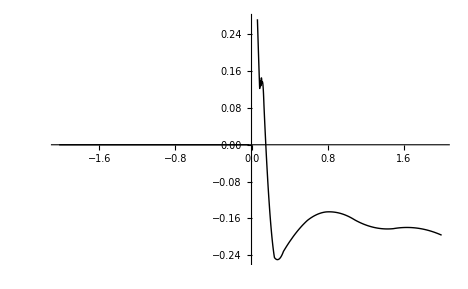

```mathematica
Plot[χFull[[-1]]'[μ],{μ,μ0-2,2}]
```

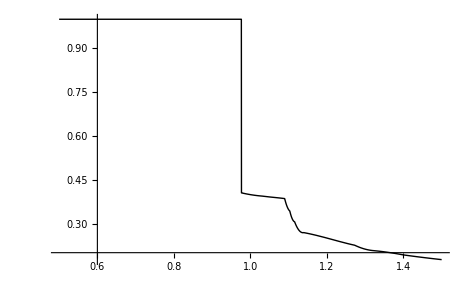

```mathematica
Plot[κ[m],{m,0.5,1.5}]
```

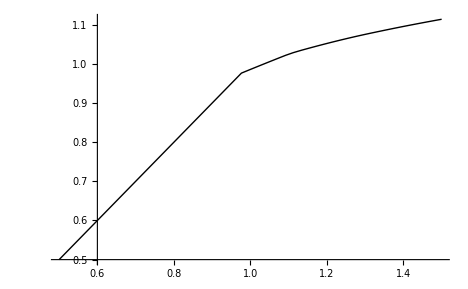

```mathematica
Plot[𝒸[m],{m,0.5,1.5}]
```

```mathematica
Plot[{nP[𝓋P[m]]-𝒸[m]},{m,mVecExcBot[[1]]/2+0.01,2.0+0*mVecExcBot[[-1]]1.5},PlotRange->All,PlotStyle->{Black,Red,Green,Blue},PlotRange->All]
```

-Graphics-

```mathematica
Animate[Plot[χFull[[n]][μ],{μ,μVecExcBot[[1]]-0.1,6(*μVecExcBot[[-1]]+0.1*)},PlotRange->{Automatic,{-0,Min[χFull[[2]][6],χFull[[Horizon]][6]]}}],{n,2,Horizon,1},AnimationRunning->False]
```

```mathematica
Animate[Plot[𝒸[m,n],{m,0.01,5},PlotRange->{Automatic,{0,2}}],{n,0,Horizon,1},AnimationRunning->False]
```

```mathematica
Plot[{cLiqExact[m],𝒸Lim[m],𝒸LinearSplineFunc[[-1]][m],cLiqOrder1Func[m],𝒸[m]},{m,1,m♮},PlotStyle->{Black,Red,Green,Blue,Yellow}]
```

-Graphics-

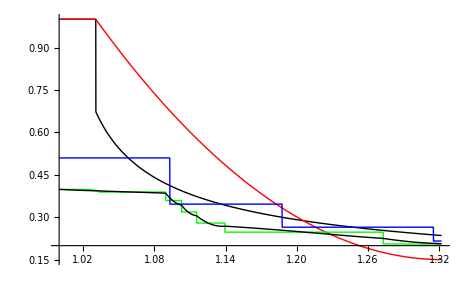

```mathematica
Plot[{κLiqExact[m],κLim[m],𝒸LinearSplineFunc[[-1]]'[m],cLiqOrder1Func'[m],κ[m]},{m,1.0,(*m♮*)mSplice},PlotStyle->{Black,Red,Green,Blue},PlotRange->All]
```

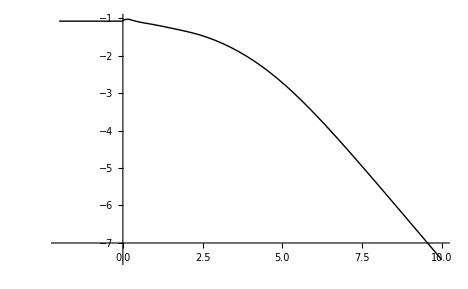

```mathematica
Plot[χ[μ],{μ,-2,10}]
```

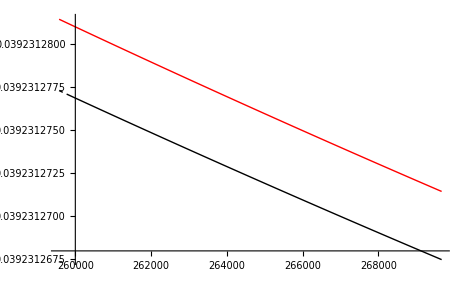

```mathematica
Plot[{κLim[m],κ[m]},{m,mLast-100,mLast+10000},PlotStyle->{Black,Red,Green},PlotRange->All]
```

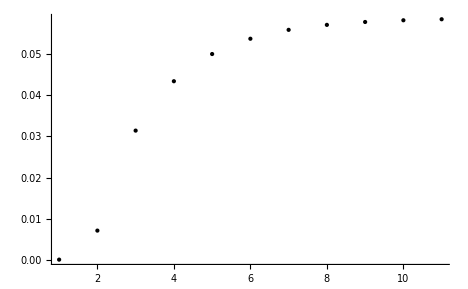

```mathematica
ListPlot[aTargetList,PlotRange->All]
```

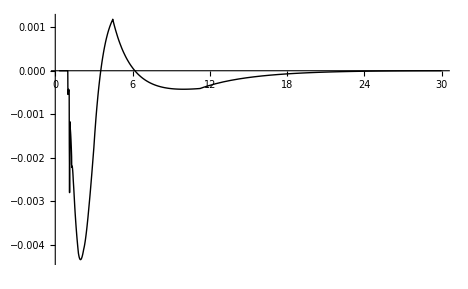

```mathematica
Plot[{κ[m,Horizon-1]-κ[m,Horizon-2]},{m,0.3,30},PlotRange->All]
```

```mathematica
(* The infinite horizon solution algorithm starts by turning off the shocks (because iteration is much faster without shocks) then turns them on again; but without the smoothing effects of shocks, it is necessary to have a much denser grid to avoid approximation problems*)

ConstructLastPeriodAsSmoothedInfHorPFLiqConstrSolnJoinedAtPeriod[3];
aGridVecExcBotSmallLength = 10;
aGridVecExcBotLargeLength = 30;
SetupGrids;

VerboseOutput=True;SolveInfHorizToToleranceAtTarget[0.0001]
```

With new shocks, adjusted Growth Patience Factor is 0.970097

0. is latest tolerance for target change.

Converged.

With new shocks, adjusted Growth Patience Factor is 0.977819

-0.0121066 is latest tolerance for target change.

-0.00569303 is latest tolerance for target change.

-0.00332599 is latest tolerance for target change.

-0.0018563 is latest tolerance for target change.

-0.00106063 is latest tolerance for target change.

Solved 10 periods.

-0.000610454 is latest tolerance for target change.

-0.000362783 is latest tolerance for target change.

-0.000215376 is latest tolerance for target change.

-0.000128613 is latest tolerance for target change.

-0.0000772623 is latest tolerance for target change.

-0.0000464639 is latest tolerance for target change.

-0.0000279851 is latest tolerance for target change.

-0.0000168413 is latest tolerance for target change.

Converged.

With new shocks, adjusted Growth Patience Factor is 0.979199

-0.00300483 is latest tolerance for target change.

Solved 20 periods.

-0.00167391 is latest tolerance for target change.

-0.00100944 is latest tolerance for target change.

-0.000614031 is latest tolerance for target change.

-0.000378586 is latest tolerance for target change.

-0.000236251 is latest tolerance for target change.

-0.000148733 is latest tolerance for target change.

-0.0000942437 is latest tolerance for target change.

-0.0000600041 is latest tolerance for target change.

-0.0000383402 is latest tolerance for target change.

Converged.

With new shocks, adjusted Growth Patience Factor is 0.979559

Solved 30 periods.

-0.00101037 is latest tolerance for target change.

-0.000569038 is latest tolerance for target change.

-0.000328312 is latest tolerance for target change.

-0.000199118 is latest tolerance for target change.

-0.00012362 is latest tolerance for target change.

-0.0000779714 is latest tolerance for target change.

Converged.

True

```mathematica
ListPlot[aTargetList,PlotRange->All]
```

-Graphics-